Prof. Elias N. Glytsis, “Introduction to Slab Dielectric Waveguides”, November 19, 2020
(http://users.ntua.gr/eglytsis/IO/Slab_Waveguides_Chapter.pdf)
上記文献のセクション「11. Multi-Layered Slab Waveguides」を実装．

```mathematica
(*========================= 初期化セル =========================*)
(*屈折率の関数を定義したノートブックを呼び出して評価*)
Clear["Global`*"]
SetDirectory[NotebookDirectory[]];
RefractiveIndexDefNotebookNames={
"Gehrsitz(2000)に基づくAlGaAsの組成比・温度・波長に依存した屈折率の導出.nb",(*nAlGaAs[(*Al組成比x*),(*温度T*),(*波長λ*)]*)
"SiO2とTiO2の室温の屈折率の導出.nb"};(*nSiO2RoomT[(*波長λ*)],nTiO2RoomT[(*波長λ*)]*)
Do[
nb=NotebookOpen[FileNameJoin[{NotebookDirectory[],RefractiveIndexDefNotebookName}]];
NotebookEvaluate[nb,EvaluationElements->"InitializationCell"];
NotebookClose[nb]
,{RefractiveIndexDefNotebookName,RefractiveIndexDefNotebookNames}]

(*DBRを構成する各層の実部の屈折率のリストを与える関数*)
DBRNList[DBRPairNum_,N1_,N2_]:=Flatten[Table[{N1,N2},DBRPairNum]]
(*実部の屈折率のリストから目標波長におけるDBRの各層の厚さのリストを与える関数*)
DBRThicknessList[RefractiveIndexList_,TargetWavelength_]:=Table[TargetWavelength/(4*Re[RefractiveIndexList[[i]]]),{i,Length[RefractiveIndexList]}]
(*任意の行列のリストからそれらすべて内積した行列を与える関数*)
ListDot[list_]:=Apply[Dot,list];(*遅い*)
(*M[1]=First[CharaMatrixList];M[n_]:=M[n]=M[n-1].CharaMatrixList[[n]]*)
ListMultiplier1[list_,partitionwidth_: 4]:=Apply[Dot,Dot@@@Partition[list,UpTo[partitionwidth]]]
ListMultiplier2[list_,partitionwidth_: 2]:=NestWhile[Dot@@@Partition[#,partitionwidth,partitionwidth,1,{}]&,list,Dimensions[#][[1]]>1&][[1]]
(*Plot画像保存用関数*)
ExpVectorImg[plot_,name_]:=Export[FileNameJoin[{NotebookDirectory[],name<>".svg"}],plot,"SVG"]
ExpBitmapImg[plot_,name_]:=Export[FileNameJoin[{NotebookDirectory[],name<>".png"}],plot,"PNG",ImageResolution-> 600]
```

```mathematica
(*FindRootの拡張．高速に複数の根を見つける．*)
(*https://community.wolfram.com/groups/-/m/t/1132423*)
Options@FindRoots=Sort@Join[Options@FindRoot,{MaxRecursion->Automatic,PerformanceGoal:>$PerformanceGoal,PlotPoints->Automatic,Debug->False,ZeroTolerance->10^-2}];
FindRoots[fun_,{var_,min_,max_},opts:OptionsPattern[]]:=Module[{PlotRules,RootRules,g,g2,pts,pts2,lpts,F,sol},(*Extract the Options*)PlotRules=Sequence@@FilterRules[Join[{opts},Options@FindRoots],Options@Plot];
RootRules=Sequence@@FilterRules[Join[{opts},Options@FindRoots],Options@FindRoot];
(*Plot the function and "mesh" the point with y-coordinate 0*)g=Normal@Plot[fun,{var,min,max},MeshFunctions->(#2&),Mesh->{{0}},Method->Automatic,Evaluate@PlotRules];
(*Get the meshes zeros*)pts=Cases[g,Point[p_]:>SetPrecision[p[[1]],OptionValue@WorkingPrecision],Infinity];
(*Get all plot points*)lpts=Join@@Cases[g,Line[p_]:>SetPrecision[p,OptionValue@WorkingPrecision],Infinity];
(*Derive the interpolated data to find other zeros*)F=Interpolation[lpts,InterpolationOrder->2];
g2=Normal@Plot[Evaluate@D[F@var,var],{var,min,max},MeshFunctions->(#2&),Mesh->{{0}},Method->Automatic,Evaluate@PlotRules];
(*Get the meshes zeros and retain only small ones*)pts2=Cases[g2,Point[p_]:>SetPrecision[p[[1]],OptionValue@WorkingPrecision],Infinity];
pts2=Select[pts2,Abs[F@#]<OptionValue@ZeroTolerance&];
pts=Join[pts,pts2];(*Join all zeros*)(*Refine zeros by passing each point through FindRoot*)If[Length@pts>0,pts=Map[FindRoot[fun,{var,#},Evaluate@RootRules]&,pts];
sol=Union@Select[pts,min≤Last@Last@#≤max&];
(*For debug purposes*)If[OptionValue@Debug,Print@Show[g,Graphics@{PointSize@0.02,Red,Point[{var,fun}/.sol]}]];
sol,If[OptionValue@Debug,Print@g];
{}]]
```

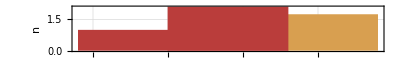

```mathematica
(*=================================================================*)
(*DBRミラーの目標波長[μm]*)TargetWL=0.575;
(*入射媒質の複素屈折率*)CoverN=1+0*nSiO2RoomT[(*波長λ*)TargetWL];
(*基板媒質の複素屈折率*)SubstrateN=1.75+0*nSiO2RoomT[(*波長λ*)TargetWL];
(*DBRミラーのペア数*)DBR1PairNum=0;DBR2PairNum=10;
(*DBR層の複素屈折率*)
DBRHighN=nTiO2RoomT[(*波長λ*)TargetWL];
DBRLowN=nSiO2RoomT[(*波長λ*)TargetWL];
(*
NList=Join[{1.4571*0.996763,1.4631*0.99677,1.4571*0.996763}];
(*各層の厚さのリスト*)
CoreR=5;
ThicknessList=Join[{(125-CoreR)/2,CoreR,(125-CoreR)/2}];
*)

(*
(*複素屈折率のリスト*)NList=Join[
DBRNList[DBR1PairNum,DBRHighN,DBRLowN],{
1,
1.49,
2.1810
},DBRNList[DBR2PairNum,DBRLowN,DBRHighN]];
(*各層の厚さのリスト*)ThicknessList=Join[
(1/4)*(TargetWL/Re[DBRNList[DBR1PairNum,DBRHighN,DBRLowN]]),{
3*0*TargetWL,
(6*0/4)*(TargetWL/1.49),
(2/2)*(TargetWL/2.1810)
},(1/4)*(TargetWL/Re[DBRNList[DBR2PairNum,DBRLowN,DBRHighN]])];*)

NList=Join[{
2.1,(*AlN*)
(*1.49,(*PMMA*)*)
0*2.1810,
0*nSiO2RoomT[(*波長λ*)λ]
}
]/.λ-> TargetWL;;
ThicknessList=Join[{
0.4,
0*(1/4)*(TargetWL/2.1),
0*(2/2)*(TargetWL/2.1810),
0*(1/4)*(TargetWL/nSiO2RoomT[(*波長λ*)λ])
}]/.λ-> TargetWL;
(*=================================================================*)
(*屈折率分布の可視化*)RefracIndexPlot=Show[
ListLinePlot[{{{-0.3,Re[CoverN]},{0,Re[CoverN]}},{{Last[Accumulate[ThicknessList]],Re[ReplaceAll[SubstrateN,λ->TargetWL] ]},{Last[Accumulate[ThicknessList]]+0.3,Re[ReplaceAll[SubstrateN,λ->TargetWL] ]}}},
PlotStyle->Directive[Opacity[0]],PlotTheme->{"Scientific","SansLabels"},Filling-> 0,FillingStyle->Automatic,ColorFunction->Function[{width,height},ColorData["DarkRainbow"][1-Mod[height,0.5]]],ColorFunctionScaling-> False],
RectangleChart[
Table[{Re[ThicknessList][[i]],ReplaceAll[Re[NList],λ->TargetWL] [[i]]},{i,Length[NList]}],
BarSpacing->None,PlotTheme->{"Scientific","SansLabels"},LabelingFunction->Automatic,ColorFunction->Function[{width,height},ColorData["DarkRainbow"][1-Mod[height,0.5]]],ColorFunctionScaling-> False
],
GridLines->Automatic,PlotRange->{0.,Automatic},PlotLabel->"Refractive index @ "<>ToString[TargetWL]<>" [μm]",FrameLabel->{"Distance from surface [μm]","n"},AspectRatio-> 1/(4*GoldenRatio),ImageSize-> Scaled[0.8]]
```

```mathematica
k[λ_,N_]:=(2π/λ)*N
k0=k[TargetWL,1];
γ[k0_,N_,β_]:=Sqrt[β^2-k0^2*N^2]
kxi[k0_,Ni_,β_]:=Sqrt[k0^2*Ni^2-β^2]
kx[i_,β_]:=kxi[k0,NList[[i]],β]
h[i_]:=ThicknessList[[i]]
Num=Length[ThicknessList];
```

TE mode

```mathematica
(*Coverから1層目*)teM0[0,β_]:=(1/2)*({{1, -1/(ⅈ*kx[1,β])}, {1, 1/(ⅈ*kx[1,β])}});
(*最終層からSubstrate*)Subscript[teM, N][Num,β_]:=
({{Exp[-ⅈ kx[Num,β]*h[Num]], Exp[+ⅈ kx[Num,β]*h[Num]]}, {-ⅈ kx[Num,β] Exp[-ⅈ kx[Num,β]*h[Num]], ⅈ kx[Num,β] Exp[+ⅈ kx[Num,β]*h[Num]]}});
(*i層目から(i+1)層目*)teMi[i_,β_]:=
(1/2)*({{Exp[-ⅈ kx[i,β]*h[i]]*(1+kx[i,β]/kx[i+1,β]), Exp[+ⅈ kx[i,β]*h[i]]*(1-kx[i,β]/kx[i+1,β])}, {Exp[-ⅈ kx[i,β]*h[i]]*(1-kx[i,β]/kx[i+1,β]), Exp[+ⅈ kx[i,β]*h[i]]*(1+kx[i,β]/kx[i+1,β])}})
teM[i_,β_]:=Which[i==0,teM0[0,β],     i==Num,Subscript[teM, N][Num,β],     True,teMi[i,β]]
```

```mathematica
Print["特性マトリックスの全内積計算時間:",AbsoluteTiming[
teMMM=ListMultiplier2[Table[teM[Num-i,β],{i,0,Num}]];
][[1]],"[s]"]
teA=({{teMMM[[1,1]]+teMMM[[1,2]]*γ[k0,CoverN,β], -1}, {teMMM[[2,1]]+teMMM[[2,2]]*γ[k0,CoverN,β], γ[k0,SubstrateN,β]}});
```

特性マトリックスの全内積計算時間:0.0011849[s]

OptionValue::nodef: FindRootsについて，未知のオプションFrameLabelがあります．

OptionValue::nodef: FindRootsについて，未知のオプションPlotRangeがあります．

OptionValue::nodef: FindRootsについて，未知のオプションPlotThemeがあります．

General::stop: この計算中に，OptionValue::nodefのこれ以上の出力は表示されません．

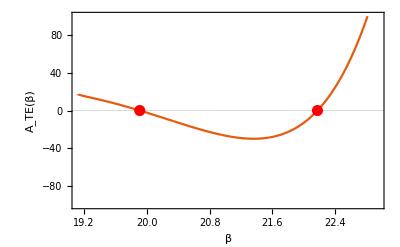

特性マトリックスの全内積計算時間:1.76957[s]

{{β→19.91},{β→22.1753}}

{-1.24345×10^-14,2.84217×10^-14}

```mathematica
(*Plot[Det[teA],{β,k0*SubstrateN,k0*Max[NList]},
FrameLabel->{"β","A_TE(β)"},PlotRange->{-100,100},
PlotTheme->{(*"Monochrome",*)"Scientific","SansLabels"}]*)
Print["特性マトリックスの全内積計算時間:",AbsoluteTiming[
βSolve=FindRoots[Re@Det[teA],{β,k0*SubstrateN,k0*Max[NList]},Debug-> True,
FrameLabel->{"β","A_TE(β)"},PlotRange->{-100,100},PlotPoints-> 50000,
PlotTheme->{(*"Monochrome",*)"Scientific","SansLabels"}]
][[1]],"[s]"]
βSolve
Re@Det[teA]/.βSolve
```

```mathematica
(*βSolve={FindRoot[Re@Det[teA],{β,13}]}*)
```

```mathematica
βList=β/.βSolve;
EsList=teA[[1,1]]/.βSolve;
βNum=Length[βList];
(*実効屈折率*)EffNList=Re[βList/k0]
xList=Prepend[Accumulate[ThicknessList],0];
```

{1.82204,2.02935}

```mathematica
teMMMi[i_,β_]:=ListMultiplier2[Table[teM[j,β],{j,i,0,-1}]]
Ey1List=Table[(teMMMi[j,βList[[βi]]].{1,γ[k0,CoverN,βList[[βi]]]})[[1]]
,{βi,Length[βList]},{j,0,Num}];
Ey2List=Table[(teMMMi[j,βList[[βi]]].{1,γ[k0,CoverN,βList[[βi]]]})[[2]]
,{βi,Length[βList]},{j,0,Num}];
EyFunc[x_,βi_]:=
If[x≤0,Exp[+γ[k0,CoverN,βList[[βi]]]*x],0]+
Sum[If[xList[[i]]<x≤ xList[[i+1]],
Ey1List[[βi,i]]*Exp[-ⅈ kx[i,βList[[βi]]]*(x-xList[[i]])]+
Ey2List[[βi,i]]*Exp[+ⅈ kx[i,βList[[βi]]]*(x-xList[[i]])],0],{i,Num}]+
If[x>Max[xList],EsList[[βi]]*Exp[-γ[k0,SubstrateN,βList[[βi]]]*(x-Max[xList])],0]
```

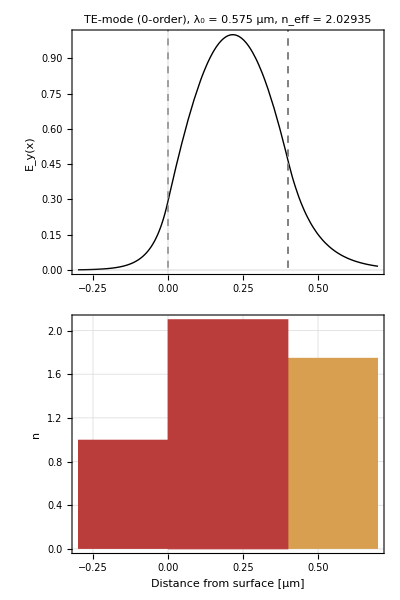

```mathematica
(*β指定．最大値が0次*)βi=Length[βList];
PlotFunc[x_,βi_]:=Re@EyFunc[x,βi]
MaxPlotFunc=Max[Table[Abs@PlotFunc[xi*(Max[xList]-Min[xList])/1000,βi],{xi,1000}]];
LinePlot=ListLinePlot[
Table[{{xList[[xi]],-MaxPlotFunc*1.2},{xList[[xi]],MaxPlotFunc*1.2}},{xi,Length[xList]}],
PlotStyle->Directive[Gray,Thickness[Tiny],Dashed]];
EyPlot=Plot[PlotFunc[x,βi]/MaxPlotFunc,{x,-0.3,Max[xList]+0.3},
PlotStyle->Directive[Black,Thickness[Large]],FrameLabel->{"","E_y(x)"},
ImageSize-> Scaled[0.8],AspectRatio-> 1/(4*GoldenRatio),
PlotRange-> Full,PlotTheme->{"Scientific","SansLabels"}];
imagePadding={{70,10},{40,2}};
EyANDnPlot=Column[{
Show[{EyPlot,LinePlot},ImagePadding->imagePadding,
PlotLabel->"TE-mode (" <> ToString[Length[βList]-βi]<>"-order), λ_0 = "<>ToString[TargetWL]<>" μm, n_eff = "<>ToString[EffNList[[βi]]] ],
Show[RefracIndexPlot,ImagePadding->imagePadding,PlotLabel->""]},Spacings-> -2.5]
```

```mathematica
ExpVectorImg[EyANDnPlot,"多層膜スラブ導波路_TEモード"]
```

C:\Users\峻之\Dropbox\00 博士研究\Mathematica\光学薄膜計算\多層膜スラブ導波路_TEモード.svg